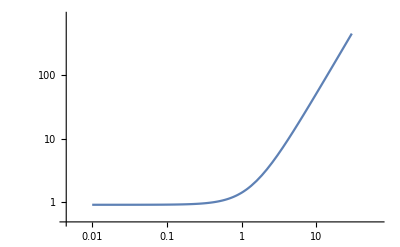

```mathematica
LogLogPlot[-Log[PDF[NormalDistribution[],x]],{x,0.01,30},PlotRange->All]
```

```mathematica
-Log[PDF[NormalDistribution[],x]]//FullSimplify
```

1/2 (-2 Log[ⅇ^(-x^2/2)]+Log[2 π])

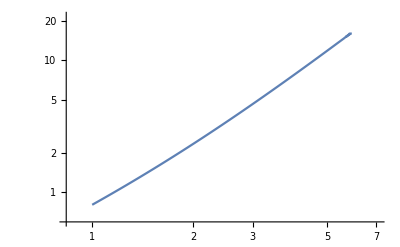

```mathematica
LogLogPlot[-Log10[1-Erf[x]],{x,1,10},PlotRange->All]
```

```mathematica
D[x Log[-Log[1-Erf[x]]],x]
```

-(2 ⅇ^(-x^2) x)/(√π (1-Erf[x]) Log[1-Erf[x]])+Log[-Log[1-Erf[x]]]

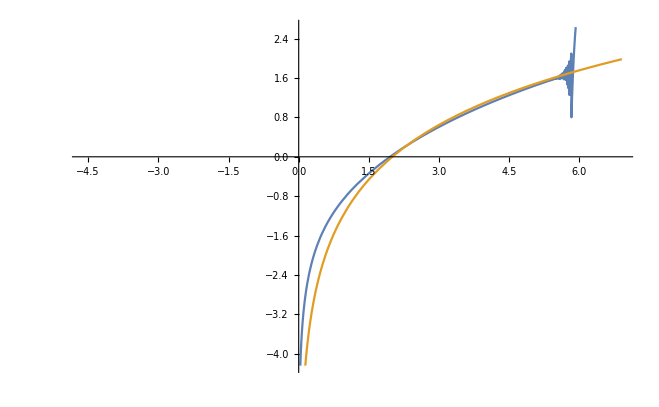

```mathematica
Plot[{(2 ⅇ^(-x^2) x)/(√π (1-Erf[x]) Log[1-Erf[x]])+Log[-Log[1-Erf[x]]],1.6Log[x/2]},{x,Log[.01],Log[1000]}]
```

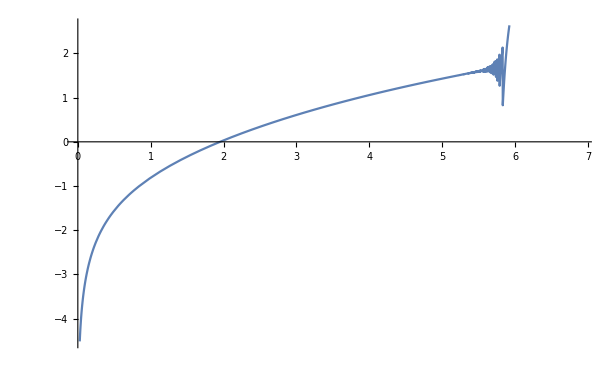

```mathematica
Plot[{(2 ⅇ^(-x^2) x)/(√π (1-Erf[x]) Log[1-Erf[x]])+Log[-Log[1-Erf[x]]]},{x,0,Log[1000]}]
```

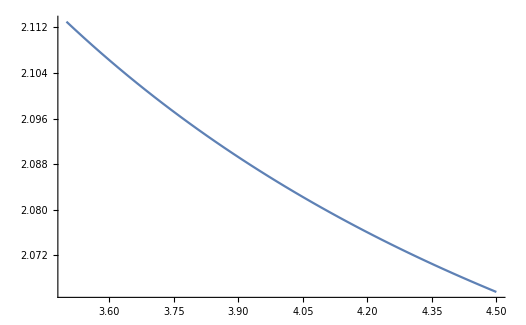

```mathematica
Plot[Log[-Log[1-Erf[x]]]/Log[x],{x,3.5,4.5}]
```

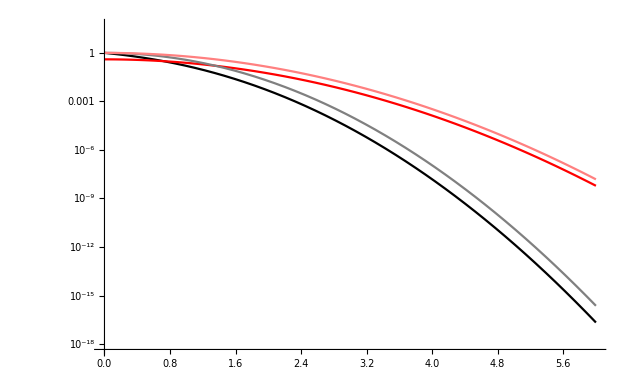

```mathematica
LogPlot[{Erfc[x],PDF[NormalDistribution[],x],Exp[-x^2],Exp[-x^2/2]},{x,0,6},PlotStyle->{Black,Red,Gray,Pink}]
```

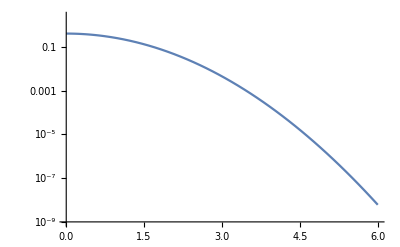

```mathematica
LogPlot[PDF[NormalDistribution[],x],{x,0,6}]
```

```mathematica
Limit[Log[Erfc[x]]+x^2+Log[x],x->Infinity]
```

-Log[π]/2

```mathematica
?Limit
```

Limit[expr,x→x_0] finds the limiting value of expr when x approaches x_0.

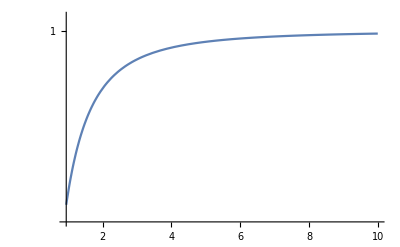

```mathematica
LogPlot[Erfc[x]/(Exp[-x^2-Log[x]]/Sqrt[Pi]),{x,0,10}]
```

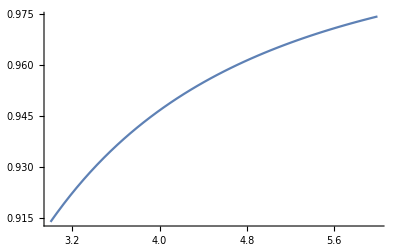

```mathematica
Plot[{(1-CDF[NormalDistribution[],x])/(PDF[NormalDistribution[],x]/(x))},{x,3,6}]
```

```mathematica
PDF[NormalDistribution[],x]/x
```

(ⅇ^(-x^2/2))/(√(2 π) x)

```mathematica
Log[10.]
```

2.30259

```mathematica
Log10[E]/2.
```

0.217147

```mathematica
1/Sqrt[2. Pi]
```

0.398942

```mathematica
.4 10^(-x^2/4.6)/x
```

(0.4 10^(-0.217391 x^2))/x

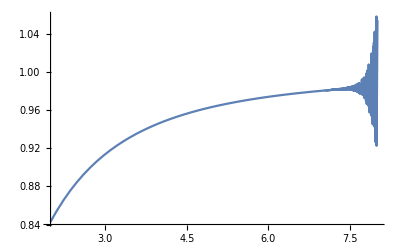

```mathematica
Plot[{(1-CDF[NormalDistribution[],x])/(Exp[-x^2/2]/(x Sqrt[2Pi]))},{x,2,8}]
```

```mathematica
2/Log[100.]
```

0.434294

```mathematica
2/(1-.997)
```

666.667

```mathematica
1/CDF[NormalDistribution[],-6.]
```

1.01359×10^9

```mathematica
1-2CDF[NormalDistribution[],-3.]
```

0.9973

```mathematica
Series[Log[1+x]-x/(1+x),{x,1,3}]
```

(-1/2+Log[2])+(x-1)/4-1/48 (x-1)^3+O[x-1]^4

```mathematica
Expand[(-1/2+Log[2])+(x-1)/4-1/48 (x-1)^3]
```

-35/48+(3 x)/16+x^2/16-x^3/48+Log[2]

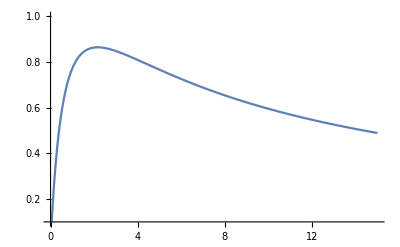

```mathematica
Plot[(Log[1+x]-x/(1+x))/(x/4),{x,0,15},PlotRange->{.1,1}]
```

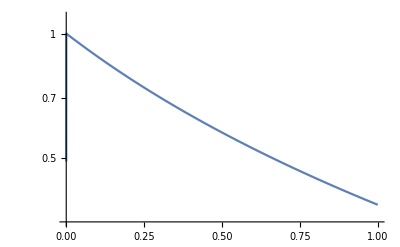

```mathematica
LogPlot[(Log[1+x]-x/(1+x))/(x^2/2),{x,0,1},PlotRange->All]
```